```mathematica
(*(*Clear all previous definitions to ensure a clean run*)ClearAll["Global`*"];*)

(*************************************************************************)
(*STEP 1:DEFINE THE "GROUND TRUTH" FUNCTION (UNCHANGED)*)
(*************************************************************************)

mfptSingleIntegral[b_?NumericQ]:=Module[{integrand,result},integrand[x_]:=Exp[-x^2/2]*(E^((x/Sqrt[2])^2) Erfc[-x/Sqrt[2]])^2;
result=NIntegrate[integrand[x],{x,-Infinity,b},WorkingPrecision->25];
(Sqrt[Pi]/(2*Sqrt[2]))*result];
mfptAnalytic[b_]:=Module[{integrand,result},integrand[x_]:=Exp[-x^2/2]*(E^((x/Sqrt[2])^2) Erfc[-x/Sqrt[2]])^2;
result=Integrate[integrand[x],{x,-Infinity,b}];
(Sqrt[Pi]/(2*Sqrt[2]))*result];
```

```mathematica
(*************************************************************************)
(*STEP 2:GENERATE OR LOAD PRE-COMPUTED DATA*)
(*************************************************************************)

(*---Parameters to adjust---*)
bMin=-6.0;
bMax=10.0; 
numPoints=4000;
SetDirectory[NotebookDirectory[]]
dataFilename="mfpt_lookup_data.mx";

(*---Check for data file,then load or generate as needed---*)
If[FileExistsQ[dataFilename],(*If file exists,load it instantly*)Print["Loading pre-computed data from \"",dataFilename,"\"..."];
{bValues,tValues}=Import[dataFilename,"MX"];,(*If file doesn't exist,run the one-time generation and save it*)Print["No data file found. Generating new data... (this may take a moment)"];
bValues=Range[bMin,bMax,(bMax-bMin)/(numPoints-1)];
tValues=Monitor[Table[mfptSingleIntegral[b],{b,bValues}],StringForm["Calculating for b = ``",N[b,4]]];
Export[dataFilename,{bValues,tValues},"MX"];
Print["Data generation complete. Saved to \"",dataFilename,"\" for future sessions."];];


(*************************************************************************)
(*STEP 3:CREATE THE FAST HYBRID FUNCTION (UNCHANGED)*)
(*************************************************************************)

splineFunction=Interpolation[Transpose[{bValues,tValues}]];
asymptoticFormula[b_]:=(Sqrt[2*Pi]/b)*Exp[b^2/2];
mfptLowerTail[b_?NumericQ]=Assuming[b<1,(Sqrt[Pi]/(2*Sqrt[2]))*Integrate[Exp[x^2/2](Series[Erfc[-x/Sqrt[2]],{x,-Infinity,5}]//Normal)^2,{x,-Infinity,b}]]//FullSimplify;
fastMFPT[b_?NumericQ]:=Which[b<bMin,mfptLowerTail[b],b>bMax,asymptoticFormula[b],True,splineFunction[b]];
fastMFPT[b_List]:=fastMFPT/@b;


(*************************************************************************)
(*STEP 4:WIDE-RANGE ACCURACY TEST (UNCHANGED)*)
(*************************************************************************)

testPoints=Table[RandomReal[{i,i+1}],{i,-12,12}];
Print[Style["\n--- Wide-Range Accuracy Test (for small b I trust the asymptotics, not the -Exact Value-) ---",Bold,14]];
results=Monitor[Table[Module[{valExact,valApprox,absError,relError},valExact=mfptSingleIntegral[b];
valApprox=fastMFPT[b];
absError=Abs[valExact-valApprox];
relError=If[valExact!=0,absError/valExact,0];
{b,valExact,valApprox,absError,relError}],{b,testPoints}],StringForm["Testing b = ``",N[b,4]]];
tableData=Prepend[results,Item[#,BaseStyle->{"Bold"}]&/@{"b","Exact Value","Approx Value","Abs. Error","Rel. Error"}];
Print[Grid[tableData,Frame->All,Spacings->{2,1},Alignment->{{Left,".",".",".","."}},Background->{None,{Lighter[Gray,.9],{White,Lighter[Blend[{Blue,Green}],.9]}}}]];
```

/Users/btw970/lin_alg/The-Lotka-Volterra-Metacommunity-Model/Infinite_pool_assembly

Loading pre-computed data from "mfpt_lookup_data.mx"...

--- Wide-Range Accuracy Test (for small b I trust the asymptotics, not the -Exact Value-) ---

b | Exact Value | Approx Value | Abs. Error | Rel. Error
-11.7466 | 2.591163280142780442382769×10^-34 | 8.11615×10^-32 | 8.09024×10^-32 | 312.224
-10.3189 | 2.621275057260638505261019×10^-27 | 6.39283×10^-25 | 6.36662×10^-25 | 242.882
-9.17952 | 2.45579523901331589239712×10^-22 | 4.78793×10^-20 | 4.76337×10^-20 | 193.965
-8.79787 | 8.575754059847779234719257×10^-21 | 1.54238×10^-18 | 1.5338×10^-18 | 178.853
-7.39888 | 1.171832669587500923900921×10^-15 | 1.17443×10^-15 | 2.599×10^-18 | 0.0022179
-6.60562 | 4.170597126135719339513565×10^-13 | 4.17251×10^-13 | 1.9106×10^-16 | 0.000458111
-5.35666 | 1.306436017443204771788169×10^-9 | 1.30644×10^-9 | 4.8929×10^-18 | 3.74523×10^-9
-4.56834 | 1.001246121657460674319279×10^-7 | 1.00125×10^-7 | 1.84902×10^-16 | 1.84672×10^-9
-3.5876 | 0.00001016459311744369661439179 | 0.0000101646 | 2.63311×10^-15 | 2.59047×10^-10
-2.49212 | 0.0006684586994468986477713827 | 0.000668459 | 2.28951×10^-13 | 3.42506×10^-10
-1.81687 | 0.005471043853669212968950166 | 0.00547104 | 1.12577×10^-12 | 2.05769×10^-10
-0.268236 | 0.2102697071271298277232988 | 0.21027 | 7.57314×10^-12 | 3.60163×10^-11
0.731703 | 1.198036947822616389179947 | 1.19804 | 5.33844×10^-11 | 4.45599×10^-11
1.50752 | 4.153502434237379978785388 | 4.1535 | 3.60218×10^-10 | 8.67262×10^-11
2.72043 | 42.86913325053240937249314 | 42.8691 | 1.69352×10^-8 | 3.95043×10^-10
3.21865 | 156.0882755838353912863887 | 156.088 | 3.40672×10^-8 | 2.18256×10^-10
4.47189 | 13078.61706467406018626121 | 13078.6 | 0.0000291967 | 2.2324×10^-9
5.00718 | 145658.8355897401903913039 | 145659. | 0.000212533 | 1.45911×10^-9
6.24304 | 1.19977654661799746603394×10^8 | 1.19978×10^8 | 0.0195768 | 1.6317×10^-10
7.14107 | 4.243399713197937839893011×10^10 | 4.2434×10^10 | 679.69 | 1.60176×10^-8
8.18011 | 1.055198126610496372288743×10^14 | 1.0552×10^14 | 1.35843×10^6 | 1.28737×10^-8
9.4336 | 5.67517238411740963778768×10^18 | 5.67517×10^18 | 2.7129×10^11 | 4.7803×10^-8
10.6465 | 9.751239907640591727471941×10^23 | 9.66362×10^23 | 8.76187×10^21 | 0.00898539
11.3317 | 1.704843866329782079147645×10^27 | 1.69135×10^27 | 1.34921×10^25 | 0.00791399
12.9193 | 3.421250759129092802245736×10^35 | 3.4005×10^35 | 2.07511×10^33 | 0.00606535

```mathematica
(************************************************************************)
```

(I found this rule because Mathematica gave me different formulae when rho -> 1 and for arbitrary rho . The requirement that they are equal for rho == 0 led to this Rule (of which Mathematica seems unaware).
Because this 2F2 converges to zero for negative arguments, It's actually better to use the negative argument form for numerical integration!

```mathematica
Rule2F2=HypergeometricPFQ[{1,1},{3/2,2},s_]:>(π Erf[√s] Erfi[√s])/(2 s)-HypergeometricPFQ[{1,1},{3/2,2},-s]
```

HypergeometricPFQ[{1,1},{3/2,2},s_]:>(π Erf[√s] Erfi[√s])/(2 s)-HypergeometricPFQ[{1,1},{3/2,2},-s]

```mathematica
Series[HypergeometricPFQ[{1,1},{3/2,2},s],{s,0,10}]
Series[HypergeometricPFQ[{1,1},{3/2,2},s]/.Rule2F2,{s,0,10}]
```

1+s/3+(4 s^2)/45+(2 s^3)/105+(16 s^4)/4725+(16 s^5)/31185+(64 s^6)/945945+(16 s^7)/2027025+(256 s^8)/310134825+(256 s^9)/3273645375+(1024 s^10)/151242416325+O[s]^11

1+s/3+(4 s^2)/45+(2 s^3)/105+(16 s^4)/4725+(16 s^5)/31185+(64 s^6)/945945+(16 s^7)/2027025+(256 s^8)/310134825+(256 s^9)/3273645375+(1024 s^10)/151242416325+O[s]^(21/2)

```mathematica
coefficient1=Assuming[n>=-2,SeriesCoefficient[(π Erf[x] Erfi[x])/(2 x^2)-HypergeometricPFQ[{1,1},{3/2,2},-x^2],{x,0,n}]//FullSimplify]
coefficient2=
Assuming[n>=-2,SeriesCoefficient[HypergeometricPFQ[{1,1},{3/2,2},x^2],{x,0,n}]//FullSimplify]

(* Should be possible to proove equality of these by demonstrating that coefficient2 satisfies the recursion equations in coefficient1 *)
```

Piecewise[{{1/2 π [2+n], n<0||Mod[n,2]>0}, {-(ⅈ^n √π)/((2+n) Gamma[(3+n)/2])+1/2 π [2+n], True}}]

Piecewise[{{(√π)/((2+n) Gamma[(3+n)/2]), Mod[n,2]==0&&n≥0}, {0, True}}]

```mathematica
Assuming[Mod[n,2]==0&&n>=0,{coefficient1,coefficient2}//FullSimplify]
%//InputForm
```

{-(ⅈ^n √π)/((2+n) Gamma[(3+n)/2])+1/2 π [2+n],(√π)/((2+n) Gamma[(3+n)/2])}

{-((I^n*Sqrt[Pi])/((2 + n)*Gamma[(3 + n)/2])) + 
  (Pi*DifferenceRoot[Function[{y, n}, 
       {-4*n*y[n] + (1 + n)*(3 + n)*(4 + n)*y[4 + n] == 
         0, y[0] == 0, y[1] == 0, y[2] == 4/Pi, y[3] == 0}]][
     2 + n])/2, Sqrt[Pi]/((2 + n)*Gamma[(3 + n)/2])}

```mathematica
mu[X_]:=rho*(x0-X) (* with rho==1 Mathematica makes simpler results *)
(*mu[X_]:=-X*)a
sigma[X_]:=sig
```

a

```mathematica
V[X_]:=Piecewise[{{0,X>=Xb},{Infinity,X<Xb}}]
fM[X_]:=X
fM2[X_]:=X^2
fM2dt[X_]:=X*(X+mu[X]*dt)
fV[X_]:=1
```

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fM[x]==0&&u[0]==0
uMRule0=DSolve[eqs,u[x],x]//Last//FullSimplify
```

x+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→x/rho+(sig C[1] (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/(√rho)+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
Series[u[x]/.uMRule0/.C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]x0/sig/Sqrt[rho]//FullSimplify,{x,Infinity,1}]//PowerExpand//Simplify
```

1/(2 rho)(-ⅈ ⅈ^(2 Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)]) π x0+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig x0)/(√rho x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) ((√π sig x0)/(√rho x)+O[1/x]^2)+(2 x+1/sig^2 x0 (ⅈ π sig^2+π sig^2 Erfi[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])-(2 x0^2)/x+O[1/x]^2))

```mathematica
c1RuleM=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]x0/sig/Sqrt[rho]
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π x0)/(√rho sig)

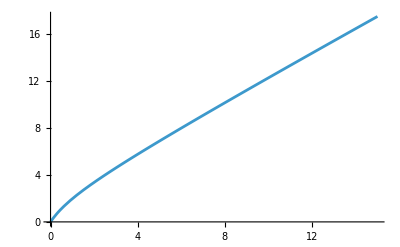

```mathematica
Plot[u[x]/.uMRule0/.c1RuleM/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uMRule=uMRule0/.c1RuleM//Simplify
```

{u[x]→x/rho+(ⅇ^((rho x0^2)/sig^2) √π x0 (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/rho+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fV[x]==0&&u[0]==0
uVRule0=Assuming[rho>0&&sig>0&&x0>0,DSolve[eqs,u[x],x]//Last//FullSimplify]/.Rule2F2//FullSimplify
```

1+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→(sig C[1] (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/(√rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
Series[u[x]/.uVRule0/.C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]/sig/Sqrt[rho]//FullSimplify,{x,Infinity,1}]//PowerExpand//Simplify
```

1/(2 rho)(-ⅈ (-1)^Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)] π+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig)/(√rho x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) ((√π sig)/(√rho x)+O[1/x]^2)+(1/sig^2(ⅈ π sig^2+π sig^2 Erfi[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])-(2 x0)/x+O[1/x]^2))

```mathematica
c1RuleV=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2]/sig/Sqrt[rho]
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π)/(√rho sig)

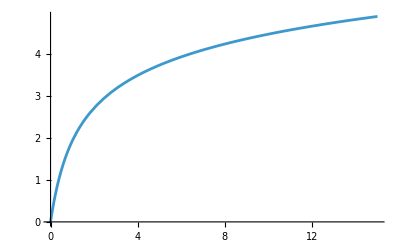

```mathematica
Plot[u[x]/.uVRule0/.c1RuleV/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uVRule=uVRule0/.c1RuleV//FullSimplify
```

{u[x]→(π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])}

```mathematica
(* Compare this to mean first passage time function: *)

u[x]/.uVRule/.x0->0
Sqrt[Pi]*Integrate[Exp[x^2](1+Erf[x]),{x,0,b},GenerateConditions->False]//FunctionExpand//Expand
```

(π Erfi[(√rho x)/sig])/(2 rho)-(x^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x^2)/sig^2])/sig^2

1/2 π Erfi[b]+b^2 HypergeometricPFQ[{1,1},{3/2,2},b^2]

```mathematica
eqs=mu[x]u'[x]+(1/2)sigma[x]^2D[u[x],{x,2}]+fM2[x]==0&&u[0]==0
uM2Rule0=Assuming[rho>0&&sig>0&&x0>0,DSolve[eqs,u[x],x]//Last//FullSimplify]/.Rule2F2//FullSimplify
```

x^2+rho (-x+x0) u'[x]+1/2 sig^2 u''[x]==0&&u[0]==0

{u[x]→1/(2 rho)(x (x+2 x0)+2 ⅇ^((rho x (x-2 x0))/sig^2) √rho sig C[1] DawsonF[(√rho (x-x0))/sig]+2 √rho sig C[1] DawsonF[(√rho x0)/sig]+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))}

```mathematica
Series[u[x]/.uM2Rule0/.C[1]->a*Sqrt[Pi]*Exp[rho x0^2/sig^2](sig^2+2 rho x0^2)/sig/Sqrt[rho]/(2rho),{x,Infinity,1}]//PowerExpand
```

ⅈ^(2 Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)]) (-(ⅈ a π sig^2)/(4 rho^2)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^2) ((a √π sig^3)/(4 rho^(5/2) x)+O[1/x]^2)+ⅈ^(2 Floor[Arg[(2 rho x x0)/sig^2-(rho x0^2)/sig^2]/(2 π)]) (-(ⅈ a π x0^2)/(2 rho)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^2) ((a √π sig x0^2)/(2 rho^(3/2) x)+O[1/x]^2)+ⅇ^((rho x^2)/sig^2-(2 (rho x0) x)/sig^2+(rho x0^2)/sig^2+O[1/x]^3) (-(√π sig (sig^2+2 rho x0^2))/(4 rho^(5/2) x)+O[1/x]^2)+(x^2/(2 rho)+(x0 x)/rho+1/(4 rho^2 sig^2)(sig^2+2 rho x0^2) (ⅈ π sig^2+2 a ⅇ^((rho x0^2)/sig^2) √π sig^2 DawsonF[(√rho x0)/sig]+2 rho x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]+sig^2 Log[rho]-2 sig^2 Log[sig]+2 sig^2 Log[x]-sig^2 PolyGamma[0,1/2])+(-sig^2 x0-2 rho x0^3)/(2 rho^2 x)+O[1/x]^2)

```mathematica
c1RuleM2=C[1]->Sqrt[Pi]*Exp[rho x0^2/sig^2](sig^2+2 rho x0^2)/sig/Sqrt[rho]/(2rho)
```

C[1]→(ⅇ^((rho x0^2)/sig^2) √π (sig^2+2 rho x0^2))/(2 rho^(3/2) sig)

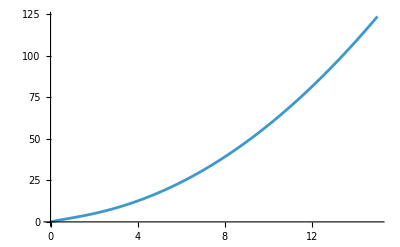

```mathematica
Plot[u[x]/.uM2Rule0/.c1RuleM2/.rho->1/.sig->1/.x0->1/2//Evaluate,{x,0,15},WorkingPrecision->100]
```

```mathematica
uM2Rule=uM2Rule0/.c1RuleM2//FullSimplify
```

{u[x]→1/(2 rho)(x (x+2 x0)+(π (sig^2+2 rho x0^2) (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))}

```mathematica
intV=integrate[(u[x]/.uVRule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
intM=integrate[(u[x]/.uMRule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
intM2=integrate[(u[x]/.uM2Rule)*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]
```

integrate[1/(√π sig)ⅇ^(-(rho (x-x0)^2)/sig^2) √rho ((π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

integrate[1/(√π sig)ⅇ^(-(rho (x-x0)^2)/sig^2) √rho (x/rho+(ⅇ^((rho x0^2)/sig^2) √π x0 (ⅇ^((rho x (x-2 x0))/sig^2) DawsonF[(√rho (x-x0))/sig]+DawsonF[(√rho x0)/sig]))/rho+1/sig^2 x0 (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

integrate[1/(2 √π √rho sig)ⅇ^(-(rho (x-x0)^2)/sig^2) (x (x+2 x0)+(π (sig^2+2 rho x0^2) (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(sig^2+2 rho x0^2) (-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2])),{x,0,∞}]

```mathematica
simpleInt=PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x]*((π (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig]))/(2 rho)+1/sig^2(-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]))/.rho->1/.sig->1//FullSimplify
```

1/(√π)ⅇ^(-(x-x0)^2) (1/2 π (Erfi[x-x0]+Erfi[x0])-(x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(x-x0)^2]+x0^2 HypergeometricPFQ[{1,1},{3/2,2},x0^2])

```mathematica
simpleIntegral[x0_]:=
fastMFPT[Sqrt[2]*x0]
```

```mathematica
simpleIntegral[0.0]-(Log[2]/2)
simpleIntegral[0]=Log[2]/2
(*WolframAlpha[ToString[%],IncludePods->"PossibleClosedForm"]*)
```

-1.11753×10^-11

Log[2]/2

```mathematica
simpleIntegral[c]//Timing
fastMFPT[Sqrt[2]*3]//Timing
mfptSingleIntegral[Sqrt[2]*3]//Timing
```

{0.000015,fastMFPT[√2 c]}

{0.00002,5117.26}

{0.020131,5117.259942826081699642779}

```mathematica
restoreRule={x0->x0*Sqrt[rho]/sig,x->x Sqrt[rho]/sig}
integrandRule=Solve[integrand==simpleInt/.HypergeometricPFQ[{1,1},{3/2,2},x0^2]->hyper/.restoreRule//Simplify,hyper]/.hyper->(HypergeometricPFQ[{1,1},{3/2,2},x0^2]/.restoreRule)//Last//FullSimplify
```

{x0→(√rho x0)/sig,x→(√rho x)/sig}

{HypergeometricPFQ[{1,1},{3/2,2},(rho x0^2)/sig^2]→1/(2 rho x0^2)(2 ⅇ^((rho (x-x0)^2)/sig^2) integrand √π sig^2-π sig^2 (Erfi[(√rho (x-x0))/sig]+Erfi[(√rho x0)/sig])+2 rho (x-x0)^2 HypergeometricPFQ[{1,1},{3/2,2},(rho (x-x0)^2)/sig^2])}

```mathematica
intVS=intV/.integrandRule//FullSimplify
intMS=intM/.integrandRule//FullSimplify
intM2S=intM2/.integrandRule//FullSimplify
```

integrate[integrand/(√rho sig),{x,0,∞}]

integrate[((ⅇ^(-(rho (x-x0)^2)/sig^2) x)/(√π)+integrand x0)/(√rho sig),{x,0,∞}]

integrate[((ⅇ^(-(rho (x-x0)^2)/sig^2) rho x (x+2 x0))/(√π)+integrand (sig^2+2 rho x0^2))/(2 rho^(3/2) sig),{x,0,∞}]

```mathematica
{intVS1,intMS1,intM2S1}=Assuming[rho>0&&sig>9,{intVS,intMS,intM2S}/.integrand->0/.integrate->Integrate]//FullSimplify
```

{0,((ⅇ^(-(rho x0^2)/sig^2) sig)/(√π)+√rho x0 (1+Erf[(√rho x0)/sig]))/(2 rho^(3/2)),((6 ⅇ^(-(rho x0^2)/sig^2) √rho sig x0)/(√π)+(sig^2+6 rho x0^2) (1+Erf[(√rho x0)/sig]))/(8 rho^2)}

```mathematica
intVS2=D[intVS[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
intMS2=D[intMS[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
intM2S2=D[intM2S[[1]],integrand]*simpleIntegral[Sqrt[rho] x0/sig]/(Sqrt[rho]/sig)
```

fastMFPT[(√2 √rho x0)/sig]/rho

(x0 fastMFPT[(√2 √rho x0)/sig])/rho

((sig^2+2 rho x0^2) fastMFPT[(√2 √rho x0)/sig])/(2 rho^2)

```mathematica
$Assumptions=SD>0 && rho>0
RuleSD=Solve[SD==sig/Sqrt[2*rho],sig]//Last
```

SD>0&&rho>0

{sig→√2 √rho SD}

```mathematica
intVSFull=intVS1+intVS2/.RuleSD//FullSimplify
intMSFull=intMS1+intMS2/.RuleSD//FullSimplify
intM2SFull=intM2S1+intM2S2/.RuleSD//FullSimplify
```

fastMFPT[x0/SD]/rho

(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD+x0+x0 Erf[x0/(√2 SD)]+2 x0 fastMFPT[x0/SD])/(2 rho)

(3 ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD x0+(SD^2+3 x0^2) (1+Erf[x0/(√2 SD)])+4 (SD^2+x0^2) fastMFPT[x0/SD])/(4 rho)

```mathematica
meanXstart=Assuming[rho>0&&sig>0,Integrate[x*PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]/Integrate[PDF[NormalDistribution[x0,sig/Sqrt[2*rho]]][x],{x,0,Infinity}]//FullSimplify//PowerExpand//FullSimplify]/.RuleSD//FullSimplify
```

x0+(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD)/(1+Erf[x0/(√2 SD)])

```mathematica
meanRichness=arrivalRate*intVSFull
meanX=Apart[arrivalRate*intMSFull/meanRichness,fastMFPT[x0/SD]]
meanX2=Apart[arrivalRate*intM2SFull/meanRichness,fastMFPT[x0/SD]]
meanXstart
(*(X*(X+mu[X]*dt)//Expand)/.X^2->meanX2/.X->meanX//FullSimplify*)
```

(arrivalRate fastMFPT[x0/SD])/rho

x0+(ⅇ^(-x0^2/(2 SD^2)) (√(2/π) SD+ⅇ^(x0^2/(2 SD^2)) x0+ⅇ^(x0^2/(2 SD^2)) x0 Erf[x0/(√2 SD)]))/(2 fastMFPT[x0/SD])

SD^2+x0^2+1/(4 fastMFPT[x0/SD])ⅇ^(-x0^2/(2 SD^2)) (ⅇ^(x0^2/(2 SD^2)) SD^2+3 √(2/π) SD x0+3 ⅇ^(x0^2/(2 SD^2)) x0^2+ⅇ^(x0^2/(2 SD^2)) SD^2 Erf[x0/(√2 SD)]+3 ⅇ^(x0^2/(2 SD^2)) x0^2 Erf[x0/(√2 SD)])

x0+(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD)/(1+Erf[x0/(√2 SD)])

```mathematica
meanFieldEquation=s-x-competition
meanEquation=s-x0-competitionMean
```

-competition+s-x

-competitionMean+s-x0

```mathematica
Solve[meanFieldEquation==0,x]//Last
x0Rule=Solve[meanEquation==0,x0]//Last
```

{x→-competition+s}

{x0→-competitionMean+s}

... now compute mean and variance of competition term following our previous work, taking into account that x0 (“y-bar”) is not a constant but correlated with mean x in the computation of the correlation of the lagged second uncentred moment. In the double sum over independent abundances and in the computation of the first moment of the competition term, x0 (“y-bar”) must be substituted by the mean of x0 over extant species (x0 * intVSFull averaged over the distribution of s); but this might cancel out and so not be needed. 

[[Also take into account that meanX2Sum might already includes the effect of a Poisson-distributed variation in species richness. But I’m not sure: its computation does not make use of the fact that species arrival and colonisation are  Poisson processes, it would go the same if arrivals were clocked. That’s still something to think about. Then again, dividing meanX2Sum by meanRichness also feels wrong. Perhaps rather make sure that meanX2Sum takes the Poisson arrival process into account, which might be different from simply multiplying with arrivalRate? One way to find this out would be to compute the corresponding quantity for fixed s and compare with out original work.]] The issue with the Poisson distributed species richness arises only for the double sum over first moments. In this case, looking at means per species and multiplying with Poisson distributed richness squared is correct. In other case, the summation over richness simply removes the division by richness from the averaging, so it is harmless.

```mathematica
normaliser=1
highProportion = .;
lowProportion = 1- highProportion
highS = 1;
lowS = 8/10;
sAveraged[expression_/;!FreeQ[expression,x0]]:=sAveraged[expression/.x0Rule]
sAveraged[expression_/;FreeQ[expression,rho|competitionMean|SD]]:=
highProportion*(expression/.s->highS)+lowProportion*(expression/.s->lowS)
sAveraged2[expression_/;Not[FreeQ[expression,s]]]:=
highProportion*(expression/.s->highS)+lowProportion*(expression/.s->lowS)
```

1

1-highProportion

```mathematica
?sAveraged
```

```mathematica
selfConsist1=-competitionMean+II*CC*sAveraged[arrivalRate*intMSFull]/.rho->rho*arrivalRate//FullSimplify
```

-competitionMean+CC II sAveraged[(ⅇ^(-(competitionMean-s)^2/(2 SD^2)) SD)/(√(2 π) rho)-1/(2 rho)(competitionMean-s) (1+Erf[(-competitionMean+s)/(√2 SD)]+2 fastMFPT[(-competitionMean+s)/SD])]

```mathematica
selfConsist2=-SD^2+II^2*CC*sAveraged[intM2SFull]/.arrivalRate->1//FullSimplify
```

-SD^2+CC II^2 sAveraged[1/(4 rho)(3 ⅇ^(-(competitionMean-s)^2/(2 SD^2)) √(2/π) (-competitionMean+s) SD+(3 (competitionMean-s)^2+SD^2) (1+Erf[(-competitionMean+s)/(√2 SD)])+4 ((competitionMean-s)^2+SD^2) fastMFPT[(-competitionMean+s)/SD])]

```mathematica
selfConsist3=Assuming[rho>0,sAveraged[x0*intMSFull]/.rho->1//FullSimplify]
```

sAveraged[(ⅇ^(-(competitionMean-s)^2/(2 SD^2)) (-competitionMean+s) SD)/(√(2 π))+1/2 (competitionMean-s)^2 (1+Erf[(-competitionMean+s)/(√2 SD)]+2 fastMFPT[(-competitionMean+s)/SD])]

```mathematica
Block[{II=4/10,CC=4/10,SESI=(1-II*CC)^2/(II^2*CC*(1-CC)),Ey=Sqrt[2/Pi]/Log[2],Ey2=(1+1/Log[4]),SPRED=SESI/Ey2,SDPRED=(Ey2/Ey)II^2*CC*(1-CC)/(II*CC*(1-II*CC))},
SPRED]//N
```

10.6748

```mathematica
table=Table[Block[{II=4/10,CC=4/10,SESI=(1-II*CC)^2/(II^2*CC*(1-CC)),Ey=Sqrt[2/Pi]/Log[2],Ey2=(1+1/Log[4]),SPRED=SESI/Ey2,SDPRED=(Ey2/Ey)II^2*CC*(1-CC)/(II*CC*(1-II*CC)),competitionMeanPRED=sAveraged[s],rhoPRED=Log[2]/SPRED},
(*Print[{rhoPRED,competitionMeanPRED,SDPRED,SPRED}//N];*)
targetFunction[a_?NumericQ,b_?NumericQ,c_?NumericQ]:={selfConsist1,selfConsist2,selfConsist3}/.{rho->a,competitionMean->b,SD->c};
fr=FindRoot[targetFunction[rho1,competitionMean1,SD1],{{rho1,rhoPRED},{competitionMean1,competitionMeanPRED},{SD1,SDPRED}},MaxIterations->1000];
(*Print[{targetFunction[rho1,competitionMean1,SD1]}/.fr];*)
fr=fr/.{rho1->rho,competitionMean1->competitionMean,SD1->SD};
fr=Prepend[fr,highProp->highProportion];
(*Print[fr];*)
fr
],{highProportion,0,1,1/100}]/.highProp->highProportion;
```

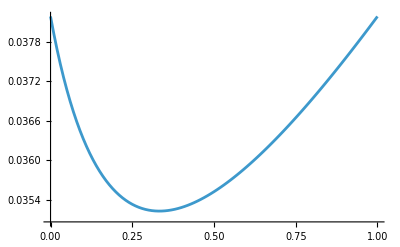

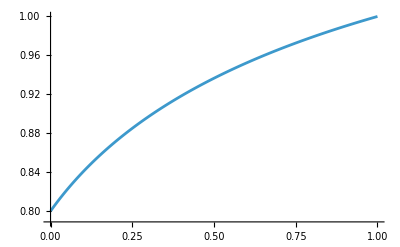

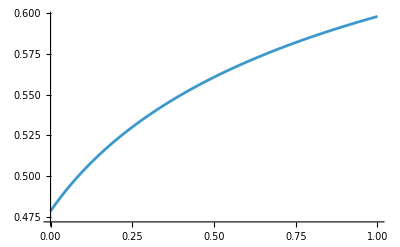

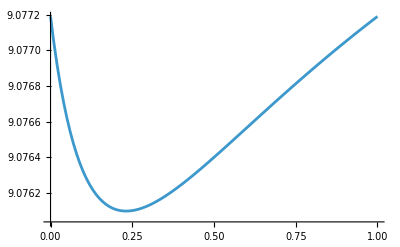

```mathematica
ListPlot[{highProportion,rho}/.table,Joined->True,PlotLegends->"rho"]
ListPlot[{highProportion,competitionMean}/.table,Joined->True,PlotLegends->"competition mean"]
ListPlot[{highProportion,SD}/.table,Joined->True,PlotLegends->"SD"]
ListPlot[{highProportion,sAveraged2[meanRichness/.x0Rule/.arrivalRate->1]}/.table,Joined->True,PlotLegends->"Richness"]
```

```mathematica
pInv[s_]=1-CDF[NormalDistribution[x0,SD]][0]/.x0Rule
```

1-1/2 Erfc[(-competitionMean+s)/(√2 SD)]

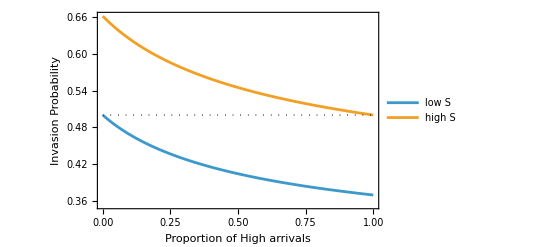

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
ListPlot[{{highProportion,pInv[lowS]}/.table,{highProportion,pInv[highS]}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Invasion Probability"}]
pInvLow=Interpolation[{highProportion,pInv[lowS]}/.table]
pInvHigh=Interpolation[{highProportion,pInv[highS]}/.table]
```

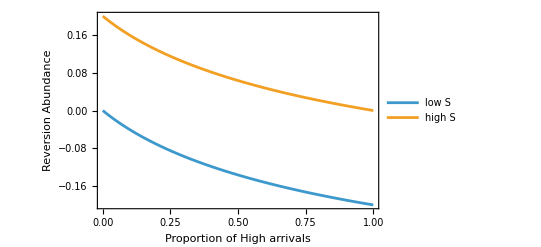

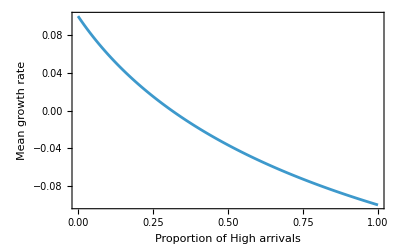

```mathematica
ListPlot[{{highProportion,s-competitionMean/.x0Rule/.s->lowS}/.table,{highProportion,s-competitionMean/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Reversion Abundance"}]
ListPlot[{highProportion,((s-competitionMean/.x0Rule/.s->lowS)+(s-competitionMean/.x0Rule/.s->highS))/2}/.table,Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean growth rate"}]
```

x0+(ⅇ^(-x0^2/(2 SD^2)) (√(2/π) SD+ⅇ^(x0^2/(2 SD^2)) x0+ⅇ^(x0^2/(2 SD^2)) x0 Erf[x0/(√2 SD)]))/(2 fastMFPT[x0/SD])

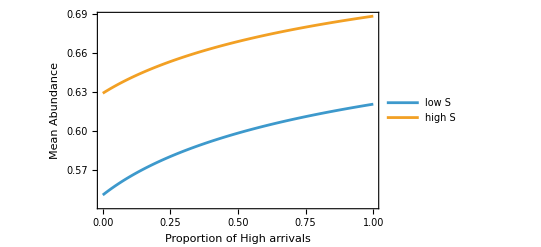

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
meanX
ListPlot[{{highProportion,meanX/.x0Rule/.s->lowS}/.table,{highProportion,meanX/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,1/2},{1,1/2}}]},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Abundance"}]
abundanceLow=Interpolation[{highProportion,meanX/.x0Rule/.s->lowS}/.table]
abundanceHigh=Interpolation[{highProportion,meanX/.x0Rule/.s->highS}/.table]
```

9.07719

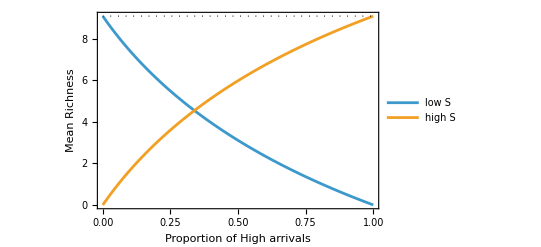

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
pureS = intVSFull/.x0Rule/.s->lowS/.table[[1]]
ListPlot[{{highProportion,(1-highProportion)*intVSFull/.x0Rule/.s->lowS}/.table,{highProportion,highProportion*intVSFull/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,pureS},{1,pureS}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Richness"}]
durationLow=Interpolation[{highProportion,(1-highProportion)*intVSFull/.x0Rule/.s->lowS}/.table]
durationHigh=Interpolation[{highProportion,highProportion*intVSFull/.x0Rule/.s->highS}/.table]
```

(ⅇ^(-x0^2/(2 SD^2)) √(2/π) SD+x0+x0 Erf[x0/(√2 SD)]+2 x0 fastMFPT[x0/SD])/(2 rho)

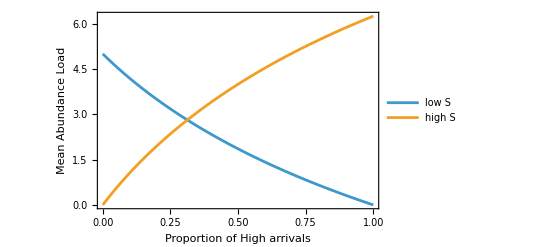

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
intMSFull
ListPlot[{{highProportion,(1-highProportion)*intMSFull/.x0Rule/.s->lowS}/.table,{highProportion,highProportion*intMSFull/.x0Rule/.s->highS}/.table},Joined->True,Epilog->{Dotted,Line[{{0,pureS},{1,pureS}}]},PlotLegends->{"low S","high S"},PlotLegends->{"low S","high S"},Frame->True,FrameLabel->{"Proportion of High arrivals", "Mean Abundance Load"}]
loadLow=Interpolation[{highProportion,(1-highProportion)*intMSFull/.x0Rule/.s->lowS}/.table]
loadHigh=Interpolation[{highProportion,highProportion*intMSFull/.x0Rule/.s->highS}/.table]
```

```mathematica
bExp=5/2(*3/2*)
rRange=1
dDensity[r_]=(bExp-1)/(Pi*rRange^2)(1+(r/rRange)^2)^(-bExp)
Integrate[(bExp-1)/(Pi*rRange^2)(1+(r/rRange)^2)^(-bExp)*r*2*Pi,{r,0,Infinity}]
```

5/2

1

3/(2 π (1+r^2)^(5/2))

1

```mathematica
NX = NY =20
environment[{x_,y_}]:=HeavisideTheta[y-(NY/4)-1/2]+1
env=Table[environment[{1,y}],{y,1,NY}]
```

20

{1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

11

11

{0.326845,0.27498,0.0437221,0.010904,0.00375334,0.0015901,0.000774667,0.000416663,0.000241156,0.000147679,0.0000945856,0.000147679,0.000241156,0.000416663,0.000774667,0.0015901,0.00375334,0.010904,0.0437221,0.27498}

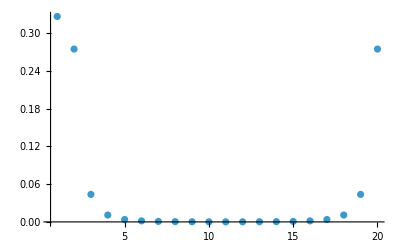

```mathematica
dKernelRaw=Table[dDensity[Sqrt[dx^2+dy^2]],{dy,-NY/2,NY/2-1},{dx,-NX/2,NX/2-1}]//N;
kernelCentreX=NX/2+1
kernelCentreY=NY/2+1
dKernelRaw[[kernelCentreX,kernelCentreY]]=0;
dKernelRaw=dKernelRaw/Total[dKernelRaw,2];
yKernel=RotateRight[Total[dKernelRaw,{2}],NY/2]
ListPlot[yKernel,PlotRange->All]
```

```mathematica
abundance1=loadHigh[1](2-env)
abundance2=loadHigh[1](env-1)
highProp=Table[1/2,NY]
oneProp=(2-env)
stepsPerInvasionAttempt=15 ; (* / 10 *)
bodyMass = 10^-4;
dispersalRate = bodyMass * 10^(-3);
offspringDispersalRate = dispersalRate/bodyMass;
```

{6.25,6.25,6.25,6.25,6.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.,0.,0.,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25,6.25}

{1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* We measure all rates in units of offspringDispersalRate! *)
For[ii=1,ii<1000,ii++,incoming1=InverseFourier[Fourier[abundance1]*Fourier[yKernel]]//Chop;
incoming2=InverseFourier[Fourier[abundance2]*Fourier[yKernel]]//Chop;
incoming1=incoming1+1/(NX*NY)/stepsPerInvasionAttempt/offspringDispersalRate;
incoming2=incoming2+1/(NX*NY)/stepsPerInvasionAttempt/offspringDispersalRate;
incoming=incoming1+incoming2;
oneProp=incoming1/incoming;
abundance1=MapThread[#1[[#2]]&,{{loadHigh[oneProp],loadLow[1-oneProp]}//Transpose,env}];
abundance2=MapThread[#1[[#2]]&,{{loadLow[oneProp],loadHigh[1-oneProp]}//Transpose,env}];
]
```

```mathematica
theoryBiomass=ListPlot[{abundance1,abundance2},PlotRange->{0,Automatic},PlotLegends->{"Biomass 1 (theory)", "Biomass 2 (theory)"},PlotMarkers->"□"]
```

-Graphics-

```mathematica
biomassSim=Import["biomass_by_type.csv", HeaderLines->{1,1}]//Transpose
```

{{5.3987,6.0003,6.1008,5.8981,5.3627,1.0779,0.5828,0.5485,0.4332,0.3613,0.4885,0.6411,0.3908,0.4922,0.451,0.3454,0.4148,0.6412,0.5901,1.236},{1.1062,0.9101,0.7093,0.7956,1.1728,5.5533,6.1697,6.219,6.1363,6.2117,6.1285,6.0736,6.1783,6.0257,6.2475,6.4131,6.2932,5.9843,6.0821,5.402}}

```mathematica
simlationBiomass=ListPlot[{biomassSim[[1]],biomassSim[[2]]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Biomass 1 (sim)", "Biomass 2 (sim)"},
PlotMarkers->"●"];
Show[theoryBiomass,simlationBiomass,PlotRange->All]
```

-Graphics-

```mathematica
(* Using this solution, now compute species-level dispersal parameter: *)pInv1=MapThread[#1[[#2]]&,{{pInvHigh[oneProp],pInvLow[1-oneProp]}//Transpose,env}]
pInv2=MapThread[#1[[#2]]&,{{pInvLow[oneProp],pInvHigh[1-oneProp]}//Transpose,env}]
alpha1=MapThread[#1[[#2]]&,{{durationHigh[oneProp],durationLow[1-oneProp]}//Transpose,env}]
alpha2=MapThread[#1[[#2]]&,{{durationLow[oneProp],durationHigh[1-oneProp]}//Transpose,env}]
meanAbundance1=abundance1/alpha1
meanAbundance2=abundance2/alpha2
rExt1=incoming1*pInv1/alpha1
rExt2=incoming2*pInv2/alpha2
(* in units of propagule attivals *)
```

{0.535176,0.520804,0.517862,0.520804,0.535176,0.394905,0.383633,0.380261,0.379074,0.378607,0.378409,0.378326,0.378304,0.378326,0.378409,0.378607,0.379074,0.380261,0.383633,0.394905}

{0.396116,0.384984,0.382719,0.384984,0.396116,0.53362,0.519051,0.514665,0.513118,0.512509,0.512251,0.512143,0.512113,0.512143,0.512251,0.512509,0.513118,0.514665,0.519051,0.53362}

{6.60589,7.57286,7.77778,7.57286,6.60589,2.36867,1.38213,1.07353,0.963341,0.919791,0.901302,0.893554,0.891406,0.893554,0.901302,0.919791,0.963341,1.07353,1.38213,2.36867}

{2.47064,1.50392,1.29905,1.50392,2.47064,6.70789,7.69467,8.00336,8.11358,8.15714,8.17563,8.18338,8.18553,8.18338,8.17563,8.15714,8.11358,8.00336,7.69467,6.70789}

{0.673044,0.679156,0.680443,0.679156,0.673044,0.603889,0.611011,0.613212,0.613995,0.614304,0.614435,0.61449,0.614506,0.61449,0.614435,0.614304,0.613995,0.613212,0.611011,0.603889}

{0.603145,0.610138,0.611604,0.610138,0.603145,0.673692,0.679921,0.681856,0.682546,0.682818,0.682933,0.682982,0.682995,0.682982,0.682933,0.682818,0.682546,0.681856,0.679921,0.673692}

{0.0790172,0.0839848,0.0853684,0.0839848,0.0790172,0.112492,0.118824,0.121584,0.122665,0.123106,0.123294,0.123373,0.123395,0.123373,0.123294,0.123106,0.122665,0.121584,0.118824,0.112492}

{0.111877,0.11775,0.119453,0.11775,0.111877,0.0795366,0.0848506,0.0870778,0.0879435,0.0882952,0.0884455,0.0885084,0.0885259,0.0885084,0.0884455,0.0882952,0.0879435,0.0870778,0.0848506,0.0795366}

```mathematica
Export["metacommunity_fields.csv",Join[{{"pColonisation1","pColonisation2","meanAbundance1","meanAbundance2","extirpationRate1","extirpationRate2"}},Transpose[{pInv1,pInv2,meanAbundance1,meanAbundance2,rExt1,rExt2}]]]
```

metacommunity_fields.csv

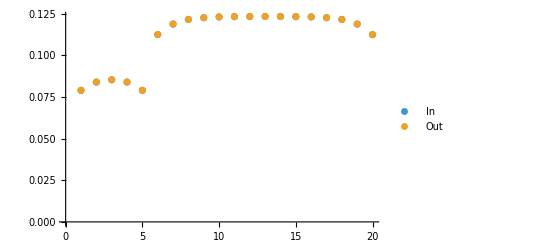

```mathematica
ListPlot[{incoming1*pInv1/alpha1,incoming1*pInv1/alpha1},PlotLegends->{"In","Out"},PlotRange->{0,All}]
```

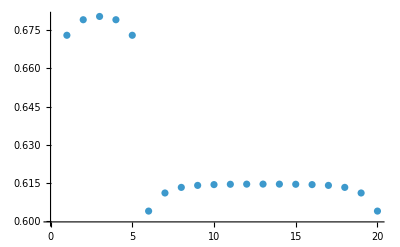

```mathematica
ListPlot[meanAbundance1]
```

```mathematica
densityX1=Table[1,{NY}]
dt=0.1;
ii=.
PrintTemporary@Dynamic@{Clock@Infinity,decayRate};
For[ii=1,ii<2000,ii++,
lastTotalX1=Total[densityX1];
abundanceX1=(densityX1/alpha1)*MapThread[#1[[#2]]&,{{loadHigh[oneProp],loadLow[1-oneProp]}//Transpose,env}];
incomingX1=InverseFourier[Fourier[abundanceX1]*Fourier[yKernel]]//Chop;
colonisationX1=incomingX1*pInv1;
densityX1+=(colonisationX1 - densityX1*rExt1)*dt;
decayRate1=Log[Total[densityX1]/lastTotalX1]/dt
]
decayRate1
1/(stepsPerInvasionAttempt*Abs[decayRate1])
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

-0.0129795

5.13631

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

-0.0110911

6.0108

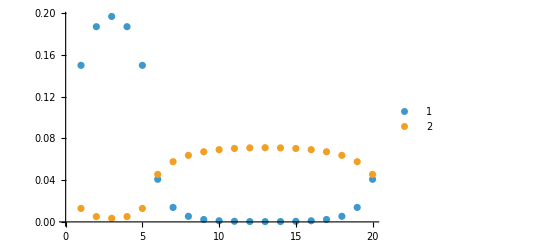

```mathematica
densityX2=Table[1,{NY}]
dt=0.1;
ii=.
PrintTemporary@Dynamic@{Clock@Infinity,decayRate};
For[ii=1,ii<2000,ii++,
lastTotalX2=Total[densityX2];
abundanceX2=(densityX2/alpha2)*MapThread[#1[[#2]]&,{{loadLow[oneProp],loadHigh[1-oneProp]}//Transpose,env}];
incomingX2=InverseFourier[Fourier[abundanceX2]*Fourier[yKernel]]//Chop;
colonisationX2=incomingX2*pInv2;
densityX2+=(colonisationX2 - densityX2*rExt2)*dt;
decayRate2=Log[Total[densityX2]/lastTotalX2]/dt
]
decayRate2
1/(stepsPerInvasionAttempt*Abs[decayRate2])
ListPlot[{densityX1/Total[densityX1],densityX2/Total[densityX2]},PlotRange->{0,Automatic},PlotLegends->{1,2}]
```

```mathematica
richnessSim=Import["richness_by_type.csv", HeaderLines->{1,1}]//Transpose
```

{{16.8,16.7,17.9,17.05,16.45,2.55,1.35,1.05,0.85,0.6,1.,0.95,0.75,0.7,1.05,0.95,1.25,1.55,1.5,2.75},{4.4,3.25,2.6,3.7,4.7,18.2,20.4,20.15,20.05,21.55,20.8,20.,21.4,20.15,20.45,19.,19.4,19.1,20.35,18.75}}

```mathematica
simlationRichness=ListPlot[{richnessSim[[1]],richnessSim[[2]],Total[richnessSim,{1}]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Mean Richness 1 (sim)", "Mean Richness 2 (sim)","Mean Combined Richness "},
PlotMarkers->"●",Frame->True,FrameLabel->{"Row", "Richness"}];
theoryRichness=ListPlot[{alpha1,alpha2,alpha1+alpha2}*2.3//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Mean Richness 1 (theo)", "Mean Richness 2 (theo)","Mean Combined Richness "},
PlotMarkers->"□",Frame->True,FrameLabel->{"Row", "Richness"}];
Show[simlationRichness,theoryRichness,PlotRange->All]
```

-Graphics-

```mathematica
richnessCDFTP=Import["richness_by_type_dcftp.csv", HeaderLines->{1,1}]//Transpose;
CDFTPRichness=ListPlot[{richnessCDFTP[[1]],richnessCDFTP[[2]],richnessCDFTP[[1]]+richnessCDFTP[[2]]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Mean Richness 1 (CDFTP)", "Mean Richness 2 (CDFTP)","Mean Combined Richness "},
PlotMarkers->"●",Frame->True,FrameLabel->{"Row", "Richness"}];
Show[CDFTPRichness,PlotRange->All]
```

-Graphics-

```mathematica
rarityCDFTP=Import["range_rarity_dcftp.csv", HeaderLines->{1,1}]//Transpose;
raritySim=Import["range_rarity.csv", HeaderLines->{1,1}]//Transpose;
rarityPlot=ListPlot[{raritySim[[1]],rarityCDFTP[[1]]}//Evaluate,PlotRange->{0,Automatic},PlotLegends->{"Simulation", "CDFTP","Mean Combined Richness "},
PlotMarkers->"●",Frame->True,FrameLabel->{"Row", "RSR"}];
Show[rarityPlot,PlotRange->All]
```

-Graphics-